# 第一题

## 尝试画图

```mathematica
(*导弹初始坐标*){M10,M20,M30}={{20000,0,2000},{19000,600,2100},{18000,-600,1900}};
(*无人机初始坐标*){FY10,FY20,FY30,FY40,FY50}={{17800,0,1800},{12000,1400,1400},{6000,-3000,700},{11000,2000,1800},{13000,-2000,1300}};
```

```mathematica
(*框架画图*)
Show[
Graphics3D[{Red,Sphere[{M10(*,M20,M30*)},100]}],
Graphics3D[{Yellow,Sphere[{FY10(*,FY20,FY30,FY40,FY50*)},100]}],
Graphics3D[InfinitePlane[{{1,0,0},{2,1,0},{3,1,0}}]],
Graphics3D[{Red,Cylinder[{{0,200,0},{0,200,10}},700]}],
Graphics3D[InfiniteLine[{FY10,{0,200,0}}]],

Axes->True,PlotRange->{{0,20000},{-3000,3000},{-1,2500}}
]
```

-Graphics3D-

```mathematica
FYSpeed=Normalize[FY10-{0,0,0}]//N
M1Speed=Normalize[M10-{0,0,0}]//N
```

{0.994926,0.,0.10061}

{0.995037,0.,0.0995037}

```mathematica
M1Move[t_]:=M10-300M1Speed t
FY1Move[t_]:=FY10-120M1Speed t
```

```mathematica
gernadMove[t_]:=If[t<1.5,FY1Move[t],If[1.5<=t<=1.5+3.6,FY1Move[t]+{0,0,0.5 9.8t^2}],FY1Move[1.5+3.6]+{0,0,0.5 9.8(1.5+3.6)^2}+{0,0,3t}]
```

```mathematica
Animate[
Show[
Graphics3D[{Red,Sphere[M1Move[t],100]}],
Graphics3D[{Yellow,Sphere[FY1Move[t],100]}],
Graphics3D[{Blue,Sphere[gernadMove[t],10]}],
Graphics3D[InfinitePlane[{{1,0,0},{2,1,0},{3,1,0}}]],
Graphics3D[{Red,Cylinder[{{0,0,0},{0,0,1000}},300]}],
Graphics3D[InfiniteLine[{FY10,{0,0,0}}]],
Graphics3D[Sphere[{0,200,0},100]],

Axes->True,PlotRange->{{0,20000},{-3000,3000},{-1,2500}}
],{t,0,50},ControlPlacement->Top]
```

```mathematica
Animate[Graphics3D[{Blue,Sphere[gernadMove[t],10]}],{t,10}]
```

```mathematica
GenerateConeEquation::usage="GenerateConeEquation[lightSource, sphereCenter, sphereRadius] 
  Generates the quadratic equation for a cone formed by a point light source projecting onto a sphere.
  - lightSource:  Coordinates {x, y, z} of the light source.
  - sphereCenter: Coordinates {x, y, z} of the sphere's center.
  - sphereRadius: The radius of the sphere (must be a positive number).
  Returns an equation of the form f[x, y, z] == 0.";

GenerateConeEquation[lightSource_List,sphereCenter_List,sphereRadius_?NumericQ]:=Module[{p,l,c,r,vecPL,vecCL,distSqCL,coneLHS},(*Assign input variables for clarity*)p={x,y,z};(*Generic point on the cone surface*)l=lightSource;
c=sphereCenter;
r=sphereRadius;
(*Pre-calculate vectors and squared distance for efficiency and readability*)vecPL=p-l;
vecCL=c-l;
distSqCL=vecCL.vecCL;
(*Check if the light source is outside the sphere*)If[distSqCL<=r^2,Message[GenerateConeEquation::invalidpos,"The light source is inside or on the surface of the sphere. No cone is formed."];
Return[$Failed];];
(*This is the core equation:((P-L).(C-L))^2-(||C-L||^2-R^2)* ||P-L||^2=0*)coneLHS=Expand[(vecPL.vecCL)^2-(distSqCL-r^2)*(vecPL.vecPL)];
(*Return the equation*)coneLHS==0]
```

```mathematica
GenerateConeEquation[{x1,y1,z1},{a,b,c},10]/.z->0//Expand//TraditionalForm
```

a^2 (-y^2)+2 a^2 y y1-a^2 y1^2-a^2 z1^2+2 a b x y-2 a b x y1-2 a b x1 y+2 a b x1 y1-2 a c x z1+2 a c x1 z1-2 a x y y1+2 a x y1^2+2 a x z1^2+2 a x1 y^2-2 a x1 y y1-b^2 x^2+2 b^2 x x1-b^2 x1^2-b^2 z1^2-2 b c y z1+2 b c y1 z1+2 b x^2 y1-2 b x x1 y-2 b x x1 y1+2 b x1^2 y+2 b y z1^2-c^2 x^2+2 c^2 x x1-c^2 x1^2-c^2 y^2+2 c^2 y y1-c^2 y1^2+2 c x^2 z1-2 c x x1 z1+2 c y^2 z1-2 c y y1 z1-x^2 y1^2-x^2 z1^2+100 x^2+2 x x1 y y1-200 x x1-x1^2 y^2+100 x1^2-y^2 z1^2+100 y^2-200 y y1+100 y1^2+100 z1^2==0

```mathematica
Show[
ContourPlot3D[300-40 x-28 x^2-40 y+32 x y-28 y^2-40 z+32 x z+32 y z-28 z^2==0,{x,-8,8},{y,-8,8},{z,0,16},PlotPoints->60],
Graphics3D[InfinitePlane[{{1,0,0},{2,1,0},{3,1,0}}]]]
```

-Graphics3D-

```mathematica
Module[{T,M,MT,MO,calpha},
T={-200,0,0}+7{Cos[th],Sin[th],0};
M={x,y,z};
MT=T-M;
MO={0,0,0}-M;
calpha=(MT.MO)/(Norm[MT] Norm[MO])

]
```

## 化简方程

(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2) √(Abs[z]^2+Abs[-200-x+7 Cos[th]]^2+Abs[-y+7 Sin[th]]^2))

```mathematica
Maximize[(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2) √(Abs[z]^2+Abs[-200-x+7 Cos[th]]^2+Abs[-y+7 Sin[th]]^2)),th]
```

Maximize[(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2) √(Abs[z]^2+Abs[-200-x+7 Cos[th]]^2+Abs[-y+7 Sin[th]]^2)),th]

```mathematica
(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2) √(Abs[z]^2+Abs[-200-x+7 Cos[th]]^2+Abs[-y+7 Sin[th]]^2))//TraditionalForm
```

(-x (7 cos(th)-x-200)-y (7 sin(th)-y)+z^2)/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2) √(Abs[-x+7 cos(th)-200]^2+Abs[7 sin(th)-y]^2+Abs[z]^2))

```mathematica
D[(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2) √(Abs[z]^2+Abs[-200-x+7 Cos[th]]^2+Abs[-y+7 Sin[th]]^2)),th]//FullSimplify
```

(2 (Abs[z]^2+Abs[200+x-7 Cos[th]]^2+Abs[y-7 Sin[th]]^2) (-7 y Cos[th]+7 x Sin[th])+14 (x (200+x)+y^2+z^2-7 x Cos[th]-7 y Sin[th]) (Abs[200+x-7 Cos[th]] Sin[th] Abs'[-200-x+7 Cos[th]]-Abs[y-7 Sin[th]] Cos[th] Abs'[-y+7 Sin[th]]))/(2 √(Abs[x]^2+Abs[y]^2+Abs[z]^2) (Abs[z]^2+Abs[200+x-7 Cos[th]]^2+Abs[y-7 Sin[th]]^2)^(3/2))

```mathematica
(2 (Abs[z]^2+Abs[200+x-7 Cos[th]]^2+Abs[y-7 Sin[th]]^2) (-7 y Cos[th]+7 x Sin[th])+14 (x (200+x)+y^2+z^2-7 x Cos[th]-7 y Sin[th]) (Abs[200+x-7 Cos[th]] Sin[th] Abs'[-200-x+7 Cos[th]]-Abs[y-7 Sin[th]] Cos[th] Abs'[-y+7 Sin[th]]))/(2 √(Abs[x]^2+Abs[y]^2+Abs[z]^2) (Abs[z]^2+Abs[200+x-7 Cos[th]]^2+Abs[y-7 Sin[th]]^2)^(3/2))//TraditionalForm
```

(14 (-7 x cos(th)-7 y sin(th)+x (x+200)+y^2+z^2) (sin(th) Abs[x-7 cos(th)+200] Abs'(7 cos(th)-x-200)-cos(th) Abs[y-7 sin(th)] Abs'(7 sin(th)-y))+2 (7 x sin(th)-7 y cos(th)) (Abs[x-7 cos(th)+200]^2+Abs[y-7 sin(th)]^2+Abs[z]^2))/(2 √(Abs[x]^2+Abs[y]^2+Abs[z]^2) (Abs[x-7 cos(th)+200]^2+Abs[y-7 sin(th)]^2+Abs[z]^2)^(3/2))

```mathematica
Solve[(2 (Abs[z]^2+Abs[200+x-7 Cos[th]]^2+Abs[y-7 Sin[th]]^2) (-7 y Cos[th]+7 x Sin[th])+14 (x (200+x)+y^2+z^2-7 x Cos[th]-7 y Sin[th]) (Abs[200+x-7 Cos[th]] Sin[th] Abs'[-200-x+7 Cos[th]]-Abs[y-7 Sin[th]] Cos[th] Abs'[-y+7 Sin[th]]))/(2 √(Abs[x]^2+Abs[y]^2+Abs[z]^2) (Abs[z]^2+Abs[200+x-7 Cos[th]]^2+Abs[y-7 Sin[th]]^2)^(3/2))==0,th]
```

Solve::nsmet: 无法利用 Solve 现有的方法求解该系统.

Solve[(2 (Abs[z]^2+Abs[200+x-7 Cos[th]]^2+Abs[y-7 Sin[th]]^2) (-7 y Cos[th]+7 x Sin[th])+14 (x (200+x)+y^2+z^2-7 x Cos[th]-7 y Sin[th]) (Abs[200+x-7 Cos[th]] Sin[th] Abs'[-200-x+7 Cos[th]]-Abs[y-7 Sin[th]] Cos[th] Abs'[-y+7 Sin[th]]))/(2 √(Abs[x]^2+Abs[y]^2+Abs[z]^2) (Abs[z]^2+Abs[200+x-7 Cos[th]]^2+Abs[y-7 Sin[th]]^2)^(3/2))==0,th]

```mathematica
□/□
```

```mathematica
Maximize[(2 (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2) (7 x Sin[th]-7 y Cos[th])+14 (x (200+x)+y^2+z^2-7 x Cos[th]-7 y Sin[th]) ((y-7 Sin[th]) Cos[th]-(200+x-7 Cos[th]) Sin[th]))/(2 Sqrt[x^2+y^2+z^2] (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2)),th]
```

Maximize[(2 (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2) (-7 y Cos[th]+7 x Sin[th])+14 (x (200+x)+y^2+z^2-7 x Cos[th]-7 y Sin[th]) (Cos[th] (y-7 Sin[th])-(200+x-7 Cos[th]) Sin[th]))/(2 √(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2)),th]

```mathematica
Expand[(2 (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2) (7 x Sin[th]-7 y Cos[th])+14 (x (200+x)+y^2+z^2-7 x Cos[th]-7 y Sin[th]) ((y-7 Sin[th]) Cos[th]-(200+x-7 Cos[th]) Sin[th]))/(2 Sqrt[x^2+y^2+z^2] (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))]
```

-(280000 y Cos[th])/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))-(1400 x y Cos[th])/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))+(19600 y Cos[th]^2)/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))+(49 x y Cos[th]^2)/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))-(343 y Cos[th]^3)/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))-(1400 y^2 Sin[th])/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))-(1400 z^2 Sin[th])/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))-(9800 x Cos[th] Sin[th])/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))-(49 x^2 Cos[th] Sin[th])/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))+(49 y^2 Cos[th] Sin[th])/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))+(343 x Cos[th]^2 Sin[th])/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))+(9800 y Sin[th]^2)/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))-(49 x y Sin[th]^2)/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))-(343 y Cos[th] Sin[th]^2)/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))+(343 x Sin[th]^3)/(√(x^2+y^2+z^2) (z^2+(200+x-7 Cos[th])^2+(y-7 Sin[th])^2)^(3/2))

```mathematica
alpha=(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(Sqrt[x^2+y^2+z^2] Sqrt[z^2+(-200-x+7 Cos[th])^2+(-y+7 Sin[th])^2])
```

(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(√(x^2+y^2+z^2) √(z^2+(-200-x+7 Cos[th])^2+(-y+7 Sin[th])^2))

```mathematica
Maximize[(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(Sqrt[x^2+y^2+z^2] Sqrt[z^2+(-200-x+7 Cos[th])^2+(-y+7 Sin[th])^2]),th]
```

Maximize[(z^2-x (-200-x+7 Cos[th])-y (-y+7 Sin[th]))/(√(x^2+y^2+z^2) √(z^2+(-200-x+7 Cos[th])^2+(-y+7 Sin[th])^2)),th]

```mathematica
expr=A (h+r*Cos[t])^2+B (h+r*Cos[t]) (k+r*Sin[t])+C (k+r*Sin[t])^2+D1 (h+r*Cos[t])+E (k+r*Sin[t])+F/.{r->7,h->-200,k->0}
```

F+D1 (-200+7 Cos[t])+A (-200+7 Cos[t])^2+7 ⅇ Sin[t]+7 B (-200+7 Cos[t]) Sin[t]+49 C Sin[t]^2

```mathematica
MaxValue[F+D1 (-200+7 Cos[t])+A (-200+7 Cos[t])^2+7 ⅇ Sin[t]+7 B (-200+7 Cos[t]) Sin[t]+49 C Sin[t]^2,t]
```

MaxValue[F+D1 (-200+7 Cos[t])+A (-200+7 Cos[t])^2+7 ⅇ Sin[t]+7 B (-200+7 Cos[t]) Sin[t]+49 C Sin[t]^2,t]

```mathematica
Solve[D[expr,t]==0,t]
```

## 画示意图(辅助思考)

### 数据/轨迹

```mathematica
(*导弹初始坐标*)missiles={M10,M20,M30}={{20000,0,2000},{19000,600,2100},{18000,-600,1900}};
(*无人机初始坐标*)drones={FY10,FY20,FY30,FY40,FY50}={{17800,0,1800},{12000,1400,1400},{6000,-3000,700},{11000,2000,1800},{13000,-2000,1300}};
(*第一题导弹速度和无人机速度*)
FYSpeed=Normalize[FY10-{0,0,Last@FY10}];
M1Speed=Normalize[M10-{0,0,0}];
M1Move[t_]:=M10-300M1Speed t
FY1Move[t_]:=FY10-120FYSpeed t
{M2Speed,M3Speed}=300Normalize[#-{0,0,0}]&/@{M20,M30};
M2Move[t_]:=M20-M2Speed t
M3Move[t_]:=M30-M3Speed t
```

### 画图

```mathematica
(*框架画图*)
frame=Show[Graphics3D[InfinitePlane[{{1,0,0},{2,1,0},{3,1,0}}]],Graphics3D[{Red,Sphere[{M10,M20,M30},100]}],
Graphics3D[{Yellow,Sphere[{FY10,FY20,FY30,FY40,FY50},100]}],Graphics3D[{Red,Cylinder[{{0,200,0},{0,200,700}},100]}],
(*Graphics3D[InfiniteLine[{FY10,{0,0,0}}]],*)Graphics3D[InfiniteLine[{M10,{0,0,0}}]],Graphics3D[InfiniteLine[{M20,{0,0,0}}]],Graphics3D[InfiniteLine[{M30,{0,0,0}}]],
Graphics3D[{Blue,Sphere[{0,200,0},100]}],Axes->True,PlotRange->{{0,20000},{-3000,3000},{-1,2500}}];
```

```mathematica
Animate[Column[{
t,
Show[frame,{
(*三个导弹的运动方程*)
Graphics3D[{Red,Sphere[M1Move[t],100]}],
Graphics3D[{Red,Sphere[M2Move[t],100]}],
Graphics3D[{Red,Sphere[M3Move[t],100]}],
(*Graphics3D[{Blue,Sphere[bombMove[t],100]}],*)
(*画指向target的线*)
Graphics3D[{Line[{M1Move[t],{0,200,0}}],Line[{M2Move[t],{0,200,0}}],Line[{M3Move[t],{0,200,0}}]}]}
(*可投放的范围的圆*)
~Join~(Graphics3D[{Blue,Opacity[0.1],Cylinder[{#,#+{0,0,1}},140t]}]&/@{FY10,FY20,FY30,FY40,FY50})
,Axes->True,Boxed->False,AxesLabel->{"x","y","z"}]
}],{t,0,70},ControlPlacement->Top,AnimationRunning->False
]
```

## 计算穿入穿出时间

```mathematica
0.5 9.8 60^2
```

17640.

```mathematica
Export["coverage.mp4",%18]
```

coverage.mp4

```mathematica
EuclideanDistance[{0,0,0},M10]/300//N
```

66.9992

```mathematica
(2 10)/(Cos[th]v)/.{th->ArcTan[1/10],v->3}//N
```

6.69992

```mathematica
200/Cos[ArcTan[19000/600]]//N
```

6336.49

```mathematica
M1Move[t]
```

{20000-(3000 t)/(√101),0,2000-(300 t)/(√101)}

```mathematica
{#,FY1Move@#}&/@Range[0,1.5,0.01]//TableForm
```

0. | 17800.
0.
1800.
0.01 | 17798.8
0.
1800.
0.02 | 17797.6
0.
1800.
0.03 | 17796.4
0.
1800.
0.04 | 17795.2
0.
1800.
0.05 | 17794.
0.
1800.
0.06 | 17792.8
0.
1800.
0.07 | 17791.6
0.
1800.
0.08 | 17790.4
0.
1800.
0.09 | 17789.2
0.
1800.
0.1 | 17788.
0.
1800.
0.11 | 17786.8
0.
1800.
0.12 | 17785.6
0.
1800.
0.13 | 17784.4
0.
1800.
0.14 | 17783.2
0.
1800.
0.15 | 17782.
0.
1800.
0.16 | 17780.8
0.
1800.
0.17 | 17779.6
0.
1800.
0.18 | 17778.4
0.
1800.
0.19 | 17777.2
0.
1800.
0.2 | 17776.
0.
1800.
0.21 | 17774.8
0.
1800.
0.22 | 17773.6
0.
1800.
0.23 | 17772.4
0.
1800.
0.24 | 17771.2
0.
1800.
0.25 | 17770.
0.
1800.
0.26 | 17768.8
0.
1800.
0.27 | 17767.6
0.
1800.
0.28 | 17766.4
0.
1800.
0.29 | 17765.2
0.
1800.
0.3 | 17764.
0.
1800.
0.31 | 17762.8
0.
1800.
0.32 | 17761.6
0.
1800.
0.33 | 17760.4
0.
1800.
0.34 | 17759.2
0.
1800.
0.35 | 17758.
0.
1800.
0.36 | 17756.8
0.
1800.
0.37 | 17755.6
0.
1800.
0.38 | 17754.4
0.
1800.
0.39 | 17753.2
0.
1800.
0.4 | 17752.
0.
1800.
0.41 | 17750.8
0.
1800.
0.42 | 17749.6
0.
1800.
0.43 | 17748.4
0.
1800.
0.44 | 17747.2
0.
1800.
0.45 | 17746.
0.
1800.
0.46 | 17744.8
0.
1800.
0.47 | 17743.6
0.
1800.
0.48 | 17742.4
0.
1800.
0.49 | 17741.2
0.
1800.
0.5 | 17740.
0.
1800.
0.51 | 17738.8
0.
1800.
0.52 | 17737.6
0.
1800.
0.53 | 17736.4
0.
1800.
0.54 | 17735.2
0.
1800.
0.55 | 17734.
0.
1800.
0.56 | 17732.8
0.
1800.
0.57 | 17731.6
0.
1800.
0.58 | 17730.4
0.
1800.
0.59 | 17729.2
0.
1800.
0.6 | 17728.
0.
1800.
0.61 | 17726.8
0.
1800.
0.62 | 17725.6
0.
1800.
0.63 | 17724.4
0.
1800.
0.64 | 17723.2
0.
1800.
0.65 | 17722.
0.
1800.
0.66 | 17720.8
0.
1800.
0.67 | 17719.6
0.
1800.
0.68 | 17718.4
0.
1800.
0.69 | 17717.2
0.
1800.
0.7 | 17716.
0.
1800.
0.71 | 17714.8
0.
1800.
0.72 | 17713.6
0.
1800.
0.73 | 17712.4
0.
1800.
0.74 | 17711.2
0.
1800.
0.75 | 17710.
0.
1800.
0.76 | 17708.8
0.
1800.
0.77 | 17707.6
0.
1800.
0.78 | 17706.4
0.
1800.
0.79 | 17705.2
0.
1800.
0.8 | 17704.
0.
1800.
0.81 | 17702.8
0.
1800.
0.82 | 17701.6
0.
1800.
0.83 | 17700.4
0.
1800.
0.84 | 17699.2
0.
1800.
0.85 | 17698.
0.
1800.
0.86 | 17696.8
0.
1800.
0.87 | 17695.6
0.
1800.
0.88 | 17694.4
0.
1800.
0.89 | 17693.2
0.
1800.
0.9 | 17692.
0.
1800.
0.91 | 17690.8
0.
1800.
0.92 | 17689.6
0.
1800.
0.93 | 17688.4
0.
1800.
0.94 | 17687.2
0.
1800.
0.95 | 17686.
0.
1800.
0.96 | 17684.8
0.
1800.
0.97 | 17683.6
0.
1800.
0.98 | 17682.4
0.
1800.
0.99 | 17681.2
0.
1800.
1. | 17680.
0.
1800.
1.01 | 17678.8
0.
1800.
1.02 | 17677.6
0.
1800.
1.03 | 17676.4
0.
1800.
1.04 | 17675.2
0.
1800.
1.05 | 17674.
0.
1800.
1.06 | 17672.8
0.
1800.
1.07 | 17671.6
0.
1800.
1.08 | 17670.4
0.
1800.
1.09 | 17669.2
0.
1800.
1.1 | 17668.
0.
1800.
1.11 | 17666.8
0.
1800.
1.12 | 17665.6
0.
1800.
1.13 | 17664.4
0.
1800.
1.14 | 17663.2
0.
1800.
1.15 | 17662.
0.
1800.
1.16 | 17660.8
0.
1800.
1.17 | 17659.6
0.
1800.
1.18 | 17658.4
0.
1800.
1.19 | 17657.2
0.
1800.
1.2 | 17656.
0.
1800.
1.21 | 17654.8
0.
1800.
1.22 | 17653.6
0.
1800.
1.23 | 17652.4
0.
1800.
1.24 | 17651.2
0.
1800.
1.25 | 17650.
0.
1800.
1.26 | 17648.8
0.
1800.
1.27 | 17647.6
0.
1800.
1.28 | 17646.4
0.
1800.
1.29 | 17645.2
0.
1800.
1.3 | 17644.
0.
1800.
1.31 | 17642.8
0.
1800.
1.32 | 17641.6
0.
1800.
1.33 | 17640.4
0.
1800.
1.34 | 17639.2
0.
1800.
1.35 | 17638.
0.
1800.
1.36 | 17636.8
0.
1800.
1.37 | 17635.6
0.
1800.
1.38 | 17634.4
0.
1800.
1.39 | 17633.2
0.
1800.
1.4 | 17632.
0.
1800.
1.41 | 17630.8
0.
1800.
1.42 | 17629.6
0.
1800.
1.43 | 17628.4
0.
1800.
1.44 | 17627.2
0.
1800.
1.45 | 17626.
0.
1800.
1.46 | 17624.8
0.
1800.
1.47 | 17623.6
0.
1800.
1.48 | 17622.4
0.
1800.
1.49 | 17621.2
0.
1800.
1.5 | 17620.
0.
1800.

```mathematica
bombMove[t_]:=Which[
0<=t<=1.5,FY1Move[t],
1.5<t<=1.5+3.6,FY1Move[t]+{0,0,-1/2 9.8(t-1.5)^2},
1.5+3.6<t<=5.1+20,FY1Move[5.1]+{0,0,-1/2 9.8(3.6)^2}+{0,0,-3(t-5.1)},
25.1<t,{-100000,-10000,-100000}
]
```

```mathematica
ListPointPlot3D[bombMove/@Range[0,25.1,0.01]]
```

-Graphics3D-

```mathematica
bombMove[9]
```

{17188.,0.,1724.8}

```mathematica
M1Move[9]//N
```

{17313.4,0.,1731.34}

```mathematica
textBlock[t_]:=If[EuclideanDistance[bombMove[t],M1Move[t]]<=10,1,0]
```

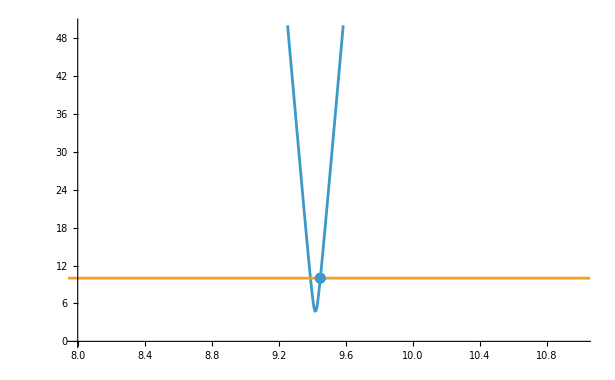

```mathematica
Show[
Plot[{EuclideanDistance[bombMove[t],M1Move[t]],10},{t,0,20},PlotRange->{{8,11},{0,50}}],
ListPlot[{{9.44809,10}}]]
```

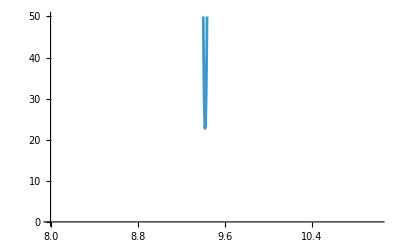

```mathematica
Plot[((FY1Move[5.1]+{0,0,-1/2 9.8(3.6)^2}+{0,0,-3(t-5.1)})[[1]]-M1Move[t][[1]])^2+((FY1Move[5.1]+{0,0,-1/2 9.8(3.6)^2}+{0,0,-3(t-5.1)})[[2]]-M1Move[t][[2]])^2+((FY1Move[5.1]+{0,0,-1/2 9.8(3.6)^2}+{0,0,-3(t-5.1)})[[3]]-M1Move[t][[3]])^2,{t,0,20},PlotRange->{{8,11},{0,50}}]
```

```mathematica
NSolve[((FY1Move[5.1]+{0,0,-1/2 9.8(3.6)^2}+{0,0,-3(t-5.1)})[[1]]-M1Move[t][[1]])^2+((FY1Move[5.1]+{0,0,-1/2 9.8(3.6)^2}+{0,0,-3(t-5.1)})[[2]]-M1Move[t][[2]])^2+((FY1Move[5.1]+{0,0,-1/2 9.8(3.6)^2}+{0,0,-3(t-5.1)})[[3]]-M1Move[t][[3]])^2==100,t,Reals]
```

{{t→9.38925},{t→9.44809}}

```mathematica
({a,b}-{c,d})^2
```

{(a-c)^2,(b-d)^2}

```mathematica
EuclideanDistance[{17188.,0.,1723.4352600000002},{17178.000895812394,0.,1717.8000895812395}]/.t->9.45358
```

11.4777

```mathematica
bombMove[t]/.t->9.45358
```

{17188.,0.,1723.44}

```mathematica
M1Move[9.45358]
```

{17178.,0.,1717.8}

```mathematica
{0,0,0}
M10
```

{0,0,0}

{20000,0,2000}

```mathematica
Distance[p1_,p2_]:=√(Tr@((p1[[#]]-p2[[#]])^2&/@{1,2,3}))
```

```mathematica
Distance[{1,1,1},{0,0,0}]
```

√3

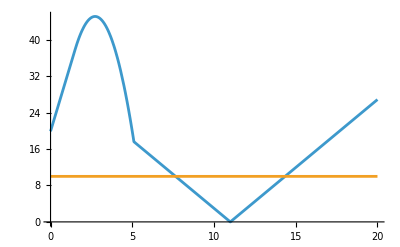

```mathematica
Plot[{√(Distance[bombMove[t],{0,0,0}]^2-(bombMove[t].Normalize[M10])^2),10},{t,0,20}]
```

```mathematica
FindRoot[√(Distance[FY1Move[5.1]+{0,0,-(9.8 3.6^2)/2}+{0,0,-3 (t-5.1)},{0,0,0}]^2-((FY1Move[5.1]+{0,0,-(9.8 3.6^2)/2}+{0,0,-3 (t-5.1)}).Normalize[M10])^2)==10,{t,7}]
```

{t→7.64871}

```mathematica
bombMove[t].Normalize[M10]
```

Which[0≤t≤1.5,FY1Move[t],1.5<t≤1.5+3.6,FY1Move[t]+{0,0,-1/2 9.8 (t-1.5)^2},1.5+3.6<t≤5.1+20,FY1Move[5.1]+{0,0,-(9.8 3.6^2)/2}+{0,0,-3 (t-5.1)},25.1<t,{-100000,-10000,-100000}].{10/(√101),0,1/(√101)}

# 第二题

## 画示意图(辅助思考)

### 数据/轨迹

```mathematica
(*导弹初始坐标*)missiles={M10,M20,M30}={{20000,0,2000},{19000,600,2100},{18000,-600,1900}};
(*无人机初始坐标*)drones={FY10,FY20,FY30,FY40,FY50}={{17800,0,1800},{12000,1400,1400},{6000,-3000,700},{11000,2000,1800},{13000,-2000,1300}};
(*第一题导弹速度和无人机速度*)
FYSpeed=Normalize[FY10-{0,0,Last@FY10}];
M1Speed=Normalize[M10-{0,0,0}];
M1Move[t_]:=M10-300M1Speed t
FY1Move[t_]:=FY10-120FYSpeed t
{M2Speed,M3Speed}=300Normalize[#-{0,0,0}]&/@{M20,M30};
M2Move[t_]:=M20-M2Speed t
M3Move[t_]:=M30-M3Speed t
bombMove[t_]:=Which[
0<=t<=1.5,FY1Move[t],
1.5<t<=1.5+3.6,FY1Move[t]+{0,0,-1/2 9.8(t-1.5)^2},
1.5+3.6<t<=5.1+20,FY1Move[5.1]+{0,0,-1/2 9.8(3.6)^2}+{0,0,-3(t-5.1)},
25.1<t,{-100000,-10000,-100000}
]
angle[v1_,v2_]:=(v1.v2)/(Norm[v1]Norm[v2])
cloud1Move[t_]:=With[{v=135.149,th=0.08895012,t1=0.87578,t2=0.9608},
Which[
t<=t1,FY10+t (v AngleVector[th]~Join~{0}),
t<=t2,FY10+t (v AngleVector[th]~Join~{0})+{0,0,-0.5 9.8t^2},
t<=t2+20,FY10+(t2)(v AngleVector[th]~Join~{0})+{0,0,-0.5 9.8(t2)^2}+{0,0,-3t},
True,Table[100000,3]
]
]
pointToLine[linep1_,linep2_,p_]:=With[{v=linep1-linep2,v1=p-linep2,ang=(p-linep2).(linep1-linep2)},
If[ang>0,√(Norm[v1]^2-Norm[(v1.Normalize[v])]^2),114514]
];
pointToLine1[linep1_,linep2_,p_]:=With[{v=linep1-linep2,v1=p-linep2,ang=(p-linep2).(linep1-linep2)},
√(Norm[v1]^2-Norm[(v1.Normalize[v])]^2)
];
```

### 画图

```mathematica
(*框架画图*)
frame=;
```

```mathematica
Manipulate[Column[{
"t="<>ToString@t,
If[
cloudDis,(pointToLine[#,M1Move[t],cloud1Move[t]]&/@Join[Table[{0,200,0}+7{Cos[th],Sin[th],0},{th,0,2Pi,0.1}],Table[{0,200,10}+7{Cos[th],Sin[th],0},{th,-Pi/2,Pi/2,0.1}]])//Max,Nothing],
"FY1-M1夹角: "<>ToString[ArcTan@@(M1Move[t][[1;;2]]-FY10[[1;;2]])//N],
"FY2-M1夹角: "<>ToString[ArcTan@@(M1Move[t][[1;;2]]-FY20[[1;;2]])//N],
"FY3-M1夹角: "<>ToString[ArcTan@@(M1Move[t][[1;;2]]-FY30[[1;;2]])//N],
Show[
(*frame*)
Show[Graphics3D[InfinitePlane[{{1,0,0},{2,1,0},{3,1,0}}]],
Graphics3D[{Blue,Opacity[0.8],Sphere[cloud1Move[t],10]}],
Graphics3D[{Yellow,Sphere[
MapThread[If[#1,#2,Nothing]&,{{showFY1,showFY2,showFY3,showFY4,showFY5},{FY10,FY20,FY30,FY40,FY50}}],100]}],Graphics3D[{Red,Cylinder[{{0,200,0},{0,200,700}},100]}],
(*Graphics3D[InfiniteLine[{FY10,{0,0,0}}]],*)Graphics3D[{
If[showM1,InfiniteLine[{M10,{0,0,0}}],Nothing],
If[showM2,InfiniteLine[{M20,{0,0,0}}],Nothing],
If[showM3,InfiniteLine[{M30,{0,0,0}}],Nothing]}],
Graphics3D[{Blue,Sphere[{0,200,0},100]}],Axes->True,PlotRange->If[zoomIn,{{17750,18000},{-30,30},{1750,1850}},{{0,20000},{-3000,3000},{-1,2500}}(**)]]
,{
(*三个导弹的运动方程*)
Graphics3D[{
If[showM1,{Red,Sphere[M1Move[t],100]},Nothing],
If[showM2,{Red,Sphere[M2Move[t],100]},Nothing],
If[showM3,{Red,Sphere[M3Move[t],100]},Nothing]
}],
(*云雾运动*)
Graphics3D[{Blue,Sphere[cloud1Move[t],10]}],
(*画指向target的线*)
Graphics3D[{
If[showM1,{Thick,Line[{M1Move[t],{0,200,0}}]},Nothing],
If[showM2,Line[{M2Move[t],{0,200,0}}],Nothing],
If[showM3,Line[{M3Move[t],{0,200,0}}],Nothing]}],
(*杂项*)
If[showLines,Graphics3D[Line[{{FY30,M1Move[t]},{FY10,M1Move[t]},{FY20,M1Move[t]}}]],Nothing],
If[showBestM1,Graphics3D[{Green,Opacity[0.1],Cylinder[{M1Move[t],M1Move[t]+{0,0,1}},1000]}],Nothing],
(*两条直线张成的平面*)
If[showPlain,ContourPlot3D[z==M10[[3]]/M10[[1]] x,{x,0,20000},{y,-3000,3000},{z,-1,2500},Mesh->None,ContourStyle->Opacity[1]],Nothing]
}
(*可投放的范围的圆*)
~Join~(Graphics3D[{{Blue,Opacity[0.1],Cylinder[{#,#+{0,0,-0.5 9.8t^2}},140t]},{Red,Opacity[0.1],Cylinder[{#,#+{0,0,-0.5 9.8t^2}},70t]}}]&/@MapThread[If[#1,#2,Nothing]&,{{showFY1,showFY2,showFY3,showFY4,showFY5},{FY10,FY20,FY30,FY40,FY50}}]
)
,Axes->False,Boxed->False,AxesLabel->{"x","y","z"}]
}],
{{t,0,"t"},0,70,0.1},
{{showM1,True,"M1"},{True,False}},{{showM2,False,"M2"},{True,False}},{{showM3,False,"M3"},{True,False}},
{{showFY1,True,"FY1"},{True,False}},{{showFY2,True,"FY2"},{True,False}},{{showFY3,True,"FY3"},{True,False}},{{showFY4,False,"FY4"},{True,False}},{{showFY5,False,"FY5"},{True,False}},{{showPlain,False,"Plain"},{True,False}},{{showLines,False,"Lines"},{True,False}},{{showBestM1,True,"M1最佳范围"},{True,False}},
{{zoomIn,False,"Zoom In"},{True,False}},{{cloudDis,False,"Cloud Distance"},{True,False}},
ControlPlacement->{Top}~Join~Table[Left,13]
]
```

## 乱七八糟

```mathematica
(pointToLine[#,M1Move[t],cloud1Move[t]]&/@Join[Table[{0,200,0}+7{Cos[th],Sin[th],0},{th,0,2Pi,0.3}],Table[{0,200,10}+7{Cos[th],Sin[th],0},{th,0,2Pi,0.3}]])//Max
```

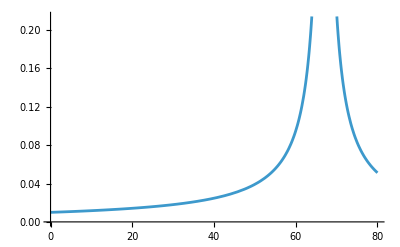

```mathematica
Plot[ArcCos@angle[{0,200,0}-M1Move[t],{0,0,0}-M1Move[t]],{t,0,80}]
```

```mathematica
ArcCos@angle[{1,1},{2,2}]
```

0

```mathematica
(*云雾运动*)
defineCloudMove[drone_,tThrow_,tBoom_]:=Which[
t<=tThrow,drone,
t<=tBoom,drone@#+{0,0,-0.5 9.8(#-tThrow)^2}&,
t<=tBoom+20,drone@tBoom+{0,0,-0.5 9.8tBoom^2}+{0,0,-3(#-tBoom)}&,
True,Table[100000,3]
]
```

```mathematica
EuclideanDistance[M1Move[14],{0,200,10}]//N
```

15900.

```mathematica
10/%//N
```

0.00062893

```mathematica
Show[
ContourPlot3D[{(x-z)^2+(y-z)^2==(1-z)^2,z==0},{x,-2,2},{y,-2,2},{z,0,1},PlotPoints->60,ContourStyle->Opacity[0.8],Mesh->None],
Graphics3D[{Opacity[1],Sphere[{0.5,0.5,0.5},0.5]}],
Graphics3D[InfiniteLine[{{2,0,1},{2,0,1}+{0,1,0.3}}]]
,PlotRange->{{-2,2},{-2,2},{0,4}}
]
```

-Graphics3D-

```mathematica
NSolve[{(x-1)^2+(y-1)^2+(z-1)^2==0.5^2,(x-z)^2+(y-z)^2==(1-z)^2},{x,y,z}]
```

NSolve::infsolns: 无穷解集的维度至少为 1. 返回解与 -(69046 x)/57903-(142003 y)/115806+(40299 z)/38602 == 1 的交集.

{{x→1.06354-1.61396 ⅈ,y→0.989958+1.6128 ⅈ,z→3.33548+0.0508436 ⅈ},{x→1.06354+1.61396 ⅈ,y→0.989958-1.6128 ⅈ,z→3.33548-0.0508436 ⅈ},{x→0.00530932-0.958256 ⅈ,y→-0.0220715+0.932537 ⅈ,z→0.93803+0.00079029 ⅈ},{x→0.00530932+0.958256 ⅈ,y→-0.0220715-0.932537 ⅈ,z→0.93803-0.00079029 ⅈ}}

```mathematica
Module[{ball,cone},
ball=(x-xt)^2+(y-yt)^2+(z-zt)^2-10;
cone=(x-x0/z0 z)^2+(y-y0/z0 z)^2-((z0-z)/z0 7)^2;
Expand/@{ball,cone}
]
```

{-10+x^2-2 x xt+xt^2+y^2-2 y yt+yt^2+z^2-2 z zt+zt^2,-49+x^2+y^2-(49 z^2)/z0^2+(x0^2 z^2)/z0^2+(y0^2 z^2)/z0^2+(98 z)/z0-(2 x x0 z)/z0-(2 y y0 z)/z0}

```mathematica
#.#&/@{{1,2,3},{4,5,6}}
```

{14,77}

```mathematica
√(7.0^2+5)
```

7.34847

```mathematica
√(10.0^2-7^2)
```

7.14143

```mathematica
(10-2(10-2))/3
```

6.18857

```mathematica
(2 √51-10)/3//N
```

1.42762

```mathematica
1.4 3
```

4.2

```mathematica
x
```

## 计算点化模型

### 近似计算时间

```mathematica
Show[
ParametricPlot3D[r{Cos[t],Sin[t],0.05t},{t,0,10Pi},{r,0,1},PlotPoints->{40, 15}],
Graphics3D[Sphere[{0.5,0.5,0.5},0.3]]]
```

-Graphics3D-

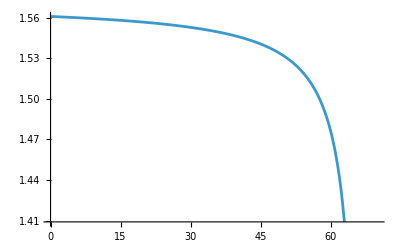

```mathematica
Plot[ArcTan[(EuclideanDistance[{0,200,0},M10]-300t)/200],{t,0,70}]
```

```mathematica
Block[{th,},
th[t_]:=ArcTan[(EuclideanDistance[{0,200,0},M10]-300t)/200];
Manipulate[
Show[
ContourPlot3D[{x,y,z}.({0,200,0}~Cross~M10)==0,{x,0,200},{y,0,200},{z,0,50},Mesh->None,ContourStyle->Opacity[0.5]],
Graphics3D[{InfiniteLine[{{0,200,0},M1Move[t]}]}],
Graphics3D[{Sphere[{50,50,30-3(t-60)},10]}]
]
,{t,60,70,0.0001}]]
```

```mathematica
Block[{d,d1,d2,al,R,r,th,oo1,th1,th2},
th[t_]:=ArcTan[(EuclideanDistance[{0,200,0},M10]-300t)/200];
d[t_]:=d0-3t;
d2[t_]:=d[t] Sin[al];d1[t_]:=d[t] Cos[al];R=10;
r=√(R^2-d2[t]^2);
oo1=√(rh^2+d1[t]^2-2d1[t] rh Cos[th0+Pi/2]);
th1=ArcCos[(rh^2+oo1^2-d1[t]^2)/(2rh oo1)];
th2=ArcSin[r/oo1];
{th2+th1,th2-th1}//FullSimplify
]
```

{ArcCos[(rh+(d0-3 t) Cos[al] Sin[th0])/(√(rh^2+(d0-3 t) Cos[al] ((d0-3 t) Cos[al]+2 rh Sin[th0])))]+ArcSin[(√(100-(d0-3 t)^2 Sin[al]^2))/(√(rh^2+(d0-3 t) Cos[al] ((d0-3 t) Cos[al]+2 rh Sin[th0])))],-ArcCos[(rh+(d0-3 t) Cos[al] Sin[th0])/(√(rh^2+(d0-3 t) Cos[al] ((d0-3 t) Cos[al]+2 rh Sin[th0])))]+ArcSin[(√(100-(d0-3 t)^2 Sin[al]^2))/(√(rh^2+(d0-3 t) Cos[al] ((d0-3 t) Cos[al]+2 rh Sin[th0])))]}

# 第三题

## 计算初始条件

```mathematica
Block[{vUp,vDown,v,vLine,vVeolocity},
vUp={0,0,3};vDown=-300Normalize[M10];
v=vUp+vDown;
vLine[t_]:={0,200,5}-M1Move[t];
vVeolocity[t_]:=v;({x,y,z}-M1Move[t]).(vLine[t]~Cross~vVeolocity[t])==0//FullSimplify//N]
```

Null^4 (903.988 x+150.748 t (-200.+y)+25. (80800.-393.95 y-401.995 z)==0.)

```mathematica
Block[{x1,y1,z1,x2,y2,z2,eqn},
{x1,y1,z1}={x0,y0,z0}+v t1 {Cos[θ],Sin[θ],0};
{x2,y2,z2}={x1,y1,z1}+{0,0,-1/2g(t2-t1)^2}+v(t2-t1){Cos[θ],Sin[θ],0};
eqn=-10<=903.987562112089 x+150.74813431681335 t (-200.+y)+25. (80800.-393.9501243788791 y-401.9950248448356 z)<=10;
eqn/.{x->x2,y->y2,z->z2,t->t2}//FullSimplify//TraditionalForm
]
```

-10≤5024.94 g t1^2-10049.9 g t1 t2+5024.94 g t2^2+t2 (150.748 t2-9848.75) v sin(θ)+903.988 t2 v cos(θ)+150.748 t2 y0-30149.6 t2+903.988 x0-9848.75 y0-10049.9 z0+2.02×10^6≤10

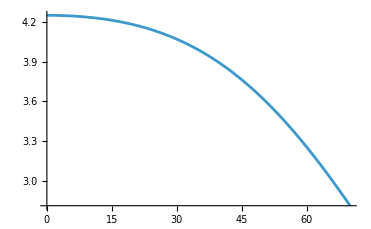
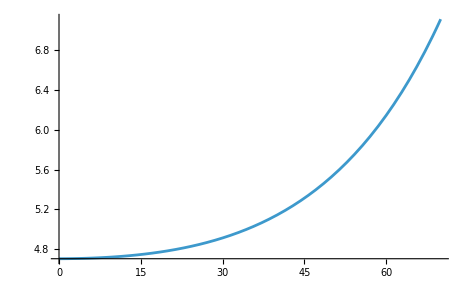
4.70745
-Graphics-
-Graphics-
-5370.22 (-20000.+298.511 t+x)+(58507.4-895.533 t) y+59702.2 (-2000.+29.8511 t+z)==0.

```mathematica
Block[{vUp,vDown,v,vLine,vVeolocity,vMove},vUp={0,0,3};vDown=-300 Normalize[M10];
v=vUp+vDown;
vLine[t_]:={0,200,5}-M1Move[t];
vVeolocity[t_]:=v;
({x,y,z}-M1Move[t]).(vLine[t]~Cross~vVeolocity[t])==0//FullSimplify//N;
vMove[t_]:=Normalize[-({0,200,0}-M1Move[1])~Cross~(vLine[t]~Cross~vVeolocity[t])];
{
({x,y,z}-M1Move[t]).(vLine[t]~Cross~vVeolocity[t])==0//FullSimplify//N}//Column;
Column[{
20/Norm[v.vMove[4]],
Plot[Norm[v.vMove[t]],{t,0,70}],
Plot[20/Norm[v.vMove[x]],{x,0,70}],
({x,y,z}-M1Move[t]).(vLine[t]~Cross~vVeolocity[t])==0
}]

]//N
```

```mathematica
MapThread
```

```mathematica
MapThread[If[#1,#2,Nothing]&,{{showFY1,showFY2,showFY3,showFY4,showFY5},{FY10,FY20,FY30,FY40,FY50}}]
```

{If[showFY1,{17800,0,1800},Nothing],If[showFY2,{12000,1400,1400},Nothing],If[showFY3,{6000,-3000,700},Nothing],If[showFY4,{11000,2000,1800},Nothing],If[showFY5,{13000,-2000,1300},Nothing]}

# 第五题

## 平面图

Show::gcomb: 无法合并 Show[,If[showM1,,Nothing],If[showM2,,Nothing],If[showM3,,Nothing],If[showFY1,,Nothing],If[showFY2,,Nothing],If[showFY3,,Nothing],If[showFY4,,Nothing],If[showFY5,,Nothing]] 中的图形对象.

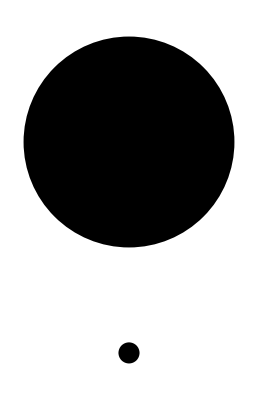
Show[-Graphics-,If[showM1,-Graphics-,Nothing],If[showM2,-Graphics-,Nothing],If[showM3,-Graphics-,Nothing],If[showFY1,-Graphics-,Nothing],If[showFY2,-Graphics-,Nothing],If[showFY3,-Graphics-,Nothing],If[showFY4,-Graphics-,Nothing],If[showFY5,-Graphics-,Nothing]]

```mathematica
{{time12,time11},{time22,time21},{time32,time31}}={{0,0},Reverse@{1.61,1.61+4.49},Reverse@{1.61+3.058,1.61+3.058+5.825}}
```

{{0,0},{6.1,1.61},{10.493,4.668}}

```mathematica
3.13579/Pi 180
```

```mathematica
179.66753243932843
```

```mathematica
cloud1Move/@{0.8728,0.9327}
```

```mathematica
{{17921.60744784337,10.866439439457283, 1800.},{17929.953330205677, 11.612199891363206,1799.982418751}}
```

```mathematica
cloud1Move[t_]:=With[{v=139.8854,th=0.08912,t1=0.8728,t2=0.9327},
Which[
t<=t1,FY10+t (v AngleVector[th]~Join~{0}),
t<=t2,FY10+t (v AngleVector[th]~Join~{0})+{0,0,-0.5 9.8(t-t1)^2},
t<=t2+20,FY10+(t2)(v AngleVector[th]~Join~{0})+{0,0,-0.5 9.8(t2-t1)^2}+{0,0,-3(t-t2)},
True,Table[100000,3]
]
];
cloud2Move[t_]:=With[{v=139,th=3.1415,t1=time21,t2=time22},
Which[
t<=t1,FY10+t (v AngleVector[th]~Join~{0}),
t<=t2,FY10+t (v AngleVector[th]~Join~{0})+{0,0,-0.5 9.8(t-t1)^2},
t<=t2+20,FY10+(t2)(v AngleVector[th]~Join~{0})+{0,0,-0.5 9.8(t2-t1)^2}+{0,0,-3(t-t2)},
True,Table[100000,3]
]
];
cloud3Move[t_]:=With[{v=139,th=3.1415,t1=time31,t2=time32},
Which[
t<=t1,FY10+t (v AngleVector[th]~Join~{0}),
t<=t2,FY10+t (v AngleVector[th]~Join~{0})+{0,0,-0.5 9.8(t-t1)^2},
t<=t2+20,FY10+(t2)(v AngleVector[th]~Join~{0})+{0,0,-0.5 9.8(t2-t1)^2}+{0,0,-3(t-t2)},
True,Table[100000,3]
]
];
```

```mathematica
coverPoint[cone_,M_,cloud_]:=pointToLine[cone,M,#]<=10&/@cloud
```

```mathematica
cp[t_]:=coverPoint[{7,200,0},M1Move[t]//N,{cloud1Move[t],cloud2Move[t],cloud3Move[t]}//N]
```

```mathematica
cp[2]
```

{False,False,False}

```mathematica
Manipulate[Column[{
"t="<>ToString@t,
If[
cloudDis,(pointToLine[#,M3Move[t],cloud1Move[t]]&/@Join[Table[{0,200,0}+7{Cos[th],Sin[th],0},{th,0,2Pi,0.1}],Table[{0,200,10}+7{Cos[th],Sin[th],0},{th,-Pi/2,Pi/2,0.1}]])//Max,Nothing],
If[
cloudDis,(pointToLine[#,M1Move[t],cloud2Move[t]]&/@Join[Table[{0,200,0}+7{Cos[th],Sin[th],0},{th,0,2Pi,0.1}],Table[{0,200,10}+7{Cos[th],Sin[th],0},{th,-Pi/2,Pi/2,0.1}]])//Max,Nothing],
If[
cloudDis,(pointToLine[#,M2Move[t],cloud3Move[t]]&/@Join[Table[{0,200,0}+7{Cos[th],Sin[th],0},{th,0,2Pi,0.1}],Table[{0,200,10}+7{Cos[th],Sin[th],0},{th,-Pi/2,Pi/2,0.1}]])//Max,Nothing],
If[show3D,
Show[
Show[
Graphics3D[InfinitePlane[{{1,0,0},{2,1,0},{3,1,0}}]],Graphics3D[{Yellow,Sphere[MapThread[If[#1,#2,Nothing]&,{{showFY1,showFY2,showFY3,showFY4,showFY5},{FY10,FY20,FY30,FY40,FY50}}],100]}],Graphics3D[{Red,Cylinder[{{0,200,0},{0,200,10}},7]}],Graphics3D[
{If[showM1,InfiniteLine[{M10,{0,0,0}}],Nothing],
If[showM2,InfiniteLine[{M20,{0,0,0}}],Nothing],
If[showM3,InfiniteLine[{M30,{0,0,0}}],Nothing]}],
(*Graphics3D[{Blue,Sphere[{0,200,0},100]}],*)Axes->True,
(*---------------------------ZOOMIN HERE------------------------------*)
PlotRange->If[zoomIn,
{{17450-140t,17900-140t},{-40-t,40-t},{1750,1850}},
{{0,20000},{-3000,3000},{-1,2500}}]
(*-------------------------------------------------------------------*)
],Join[{
Graphics3D[{
If[showM1,{Red,Sphere[M1Move[t],100]},Nothing],
If[showM2,{Red,Sphere[M2Move[t],100]},Nothing],
If[showM3,{Red,Sphere[M3Move[t],100]},Nothing]
}],
(*---------------------------CLoud HERE------------------------------*)
Graphics3D[{
{Purple,Opacity[0.8],Sphere[cloud1Move[t],10]},
{Red,Opacity[0.8],Sphere[cloud2Move[t],10]},
{Green,Opacity[0.8],Sphere[cloud3Move[t],10]}
}],
(*-------------------------------------------------------------------*)
Graphics3D[{
If[showM1,{Line[{M1Move[t],{0,200,0}}]},Nothing],
If[showM2,Line[{M2Move[t],{0,200,0}}],Nothing],
If[showM3,Line[{M3Move[t],{0,200,0}}],Nothing]}],If[showLines,Graphics3D[Line[{{FY30,M1Move[t]},{FY10,M1Move[t]},{FY20,M1Move[t]}}]],Nothing],If[showBestM1,Graphics3D[{Green,Opacity[0.1],Cylinder[{M1Move[t],M1Move[t]+{0,0,1}},1000]}],Nothing],If[showBestM3,Graphics3D[{Green,Opacity[0.1],Cylinder[{M3Move[t],M3Move[t]+{0,0,1}},1000]}],Nothing],If[showPlain,ContourPlot3D[z==(M10⟦3⟧ x)/M10⟦1⟧,{x,0,20000},{y,-3000,3000},{z,-1,2500},Mesh->None,ContourStyle->Opacity[1]],Nothing]},(Graphics3D[{{Blue,Opacity[0.1],Cylinder[{#1,#1+{0,0,-0.5 9.8 t^2}},140 t]},{Red,Opacity[0.1],Cylinder[{#1,#1+{0,0,-0.5 9.8 t^2}},70 t]}}]&)/@MapThread[If[#1,#2,Nothing]&,{{showFY1,showFY2,showFY3,showFY4,showFY5},{FY10,FY20,FY30,FY40,FY50}}]],Axes->False,Boxed->False,AxesLabel->{"x","y","z"}],
(*----------------------------上3D 下2D 分割线-----------------------------------------------*)
Show[{
(*Frame*)
(*真目标&假目标*)Graphics[{Disk[{0,200},100],Disk[{0,0},10],Rectangle[{0,-3000},{20000,-3000}]}],
(*导弹的若干*)
If[showM1,Graphics[{
Line[{{0,0},M10[[1;;2]]}],{Line[{{0,200},M1Move[t][[1;;2]]}]},{Red,Disk[M1Move[t][[1;;2]],If[zoomIn,80,100]]}(*,Circle[M1Move[t]⟦1;;2⟧,100]*)
}],Nothing],
If[showM2,Graphics[{
Line[{{0,0},M20[[1;;2]]}],{Line[{{0,200},M2Move[t][[1;;2]]}]},{Red,Disk[M2Move[t][[1;;2]],100]},{Thin,Circle[M2Move[t][[1;;2]],100]}
}],Nothing],
If[showM3,Graphics[{
Line[{{0,0},M30[[1;;2]]}],{Line[{{0,200},M3Move[t][[1;;2]]}]},{Red,Disk[M3Move[t][[1;;2]],100]},Circle[M3Move[t][[1;;2]],100]
}],Nothing],
If[showBestM1,Graphics[{{Green,Opacity[0.1],Disk[M1Move[t][[1;;2]],1000]},Circle[M1Move[t][[1;;2]],1000]}],Nothing],
If[showBestM2,Graphics[{{Green,Opacity[0.1],Disk[M2Move[t][[1;;2]],1000]},Circle[M2Move[t][[1;;2]],1000]}],Nothing],If[showBestM3,Graphics[{{Green,Opacity[0.1],Disk[M3Move[t][[1;;2]],1000]},Circle[M3Move[t][[1;;2]],1000]}],Nothing],
(*无人机的若干*)
If[showFY1,Graphics[{{DarkYellow,Disk[FY10[[1;;2]],If[zoomIn,80,100]]},{Blue,Opacity[0.1],Disk[FY10[[1;;2]],140 t]},{Red,Opacity[0.3],Disk[FY10[[1;;2]],70 t]},Circle[FY10[[1;;2]],70 t],Circle[FY10[[1;;2]],140 t]}],Nothing],If[showFY2,Graphics[{{DarkYellow,Disk[FY20[[1;;2]],100]},{Blue,Opacity[0.1],Disk[FY20[[1;;2]],140 t]},{Red,Opacity[0.3],Disk[FY20[[1;;2]],70 t]},Circle[FY20[[1;;2]],70 t],Circle[FY20[[1;;2]],140 t]}],Nothing],If[showFY3,Graphics[{{DarkYellow,Disk[FY30[[1;;2]],100]},{Blue,Opacity[0.1],Disk[FY30[[1;;2]],140 t]},{Red,Opacity[0.3],Disk[FY30[[1;;2]],70 t]},Circle[FY30[[1;;2]],70 t],Circle[FY30[[1;;2]],140 t]}],Nothing],If[showFY4,Graphics[{{DarkYellow,Disk[FY40[[1;;2]],100]},{Blue,Opacity[0.1],Disk[FY40[[1;;2]],140 t]},{Red,Opacity[0.3],Disk[FY40[[1;;2]],70 t]},Circle[FY40[[1;;2]],70 t],Circle[FY40[[1;;2]],123.88 t],Circle[FY40[[1;;2]],140 t]}],Nothing],If[showFY5,Graphics[{{DarkYellow,Disk[FY50[[1;;2]],100]},{Blue,Opacity[0.1],Disk[FY50[[1;;2]],140 t]},{Red,Opacity[0.3],Disk[FY50[[1;;2]],70 t]},Circle[FY50[[1;;2]],70 t],Circle[FY50[[1;;2]],140 t]}],Nothing],
Graphics[Point[{{11036.317636923784,64.62003741495906},{11043.581712962801,-322.48519308527307}}]],
ContourPlot[{x==18000,x==14000,x==7000},{x,0,20000},{y,-3000,3000},ContourStyle->{Thin}]
},
PlotRange->If[zoomIn,{{15800,19800},{-2500,2500}},{{0,20000},{-3000,3000}},Axes->{True,True}]]
]}],
{{t,0,"t"},0,100,0.1},{{showM1,True,"M1"},{True,False}},{{showM2,True,"M2"},{True,False}},{{showM3,True,"M3"},{True,False}},{{showFY1,False,"FY1"},{True,False}},{{showFY2,False,"FY2"},{True,False}},{{showFY3,False,"FY3"},{True,False}},{{showFY4,True,"FY4"},{True,False}},{{showFY5,False,"FY5"},{True,False}},{{showPlain,False,"Plain"},{True,False}},{{showLines,False,"Lines"},{True,False}},{{showBestM1,False,"M1最佳范围"},{True,False}},{{showBestM2,False,"M2最佳范围"},{True,False}},{{showBestM3,False,"M3最佳范围"},{True,False}},{{zoomIn,False,"Zoom In"},{True,False}},{{cloudDis,False,"Cloud Distance"},{True,False}},{{show3D,True,"3D"},{True,False}},ControlPlacement->Join[{Top},Table[Left,16]]
]
```

```mathematica
M3Move[t]
```

{18000-(54000 t)/(√32797),-600+(1800 t)/(√32797),1900-(5700 t)/(√32797)}

## 计算初值

### FY3 守家

```mathematica
Block[{t0,t02,t03,la,v,d0,hmin,p,p2,p3,t11,t12,t22,t21,t32,t31,h0,h2,h3,dronep,dir},
v=140;
t0=EuclideanDistance[{0,200},FY30[[;;2]]]/v;
p={0,200};
h0=√51;
d0=EuclideanDistance[p[[;;2]],FY30[[;;2]]];
dir=Normalize[p-FY30[[;;2]]];
(*第一枚的t1,t2*)
d0=EuclideanDistance[p[[;;2]],FY30[[;;2]]];
{t12,t11}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t0-t2)==(FY30[[3]]-h0),t2 v==d0},{t1,t2}][[1]];
{t22,t21}={t12,t11}+{0,1};
{t32,t31}={t22,t21}+{0,1};
(*---------------------------输出-------------------------*)
{{t12,t11},{t22,t21},{t32,t31},ArcTan@@dir//N,v}
]
```

{{48.5714,36.6803},{48.5714,37.6803},{48.5714,38.6803},2.65164,140}

```mathematica
{{time12,time11},{time22,time21},{time32,time31}}=%[[;;3]]
```

{{48.5714,36.6803},{48.5714,37.6803},{48.5714,38.6803}}

### FY3 贪心

```mathematica
Block[{t0,t02,t03,la,v,d0,hmin,p,p2,p3,t11,t12,t22,t21,t32,t31,h0,h2,h3,dronep,dir},
v=125;
t0=FindRoot[pointToLine1[{0,200},M3Move[t][[;;2]],FY30[[;;2]]]==v t,{t,12.7}][[1,2]];
p=Re/@Last/@NSolve[{(-FY30[[1]]+x)^2+(-FY30[[2]]+y)^2==v^2t0^2,(y-200)/x==(M3Move[t0][[2]]-200)/(M3Move[t0][[1]])},{x,y}][[1]];
h0=p[[1]]/(M3Move[t0][[1]])M3Move[t0][[3]];
d0=EuclideanDistance[p[[;;2]],FY30[[;;2]]];
dir=Normalize[p-FY30[[;;2]]];
(*第一枚的t1,t2*)
d0=EuclideanDistance[p[[;;2]],FY30[[;;2]]];
{t12,t11}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t0-t2)==(FY30[[3]]-h0),t2 v==d0},{t1,t2}][[1]];
(*---------------------------1点结束-------------------------*)

p2=Last/@NSolve[{(x-FY30[[1]])/(y-FY30[[2]])==dir[[1]]/dir[[2]],(y-200)/x==(M1Move[1/v EuclideanDistance[{x,y},FY30[[;;2]]]][[2]]-200)/M1Move[EuclideanDistance[{x,y},FY30[[;;2]]]/v][[1]]},{x,y}][[2]];
t02=EuclideanDistance[p2,FY30[[;;2]]]/v;
h2=p2[[1]]/(M1Move[t02][[1]])M1Move[t02][[3]]+10;
d0=EuclideanDistance[p2[[;;2]],FY30[[;;2]]];
{t22,t21}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t02-t2)==(FY30[[3]]-h2),t2 v==d0},{t1,t2}][[1]];
(*---------------------------2点结束-------------------------*)
p3=Last/@NSolve[{(x-FY30[[1]])/(y-FY30[[2]])==dir[[1]]/dir[[2]],(y-200)/x==(M2Move[1/v EuclideanDistance[{x,y},FY30[[;;2]]]][[2]]-200)/M2Move[EuclideanDistance[{x,y},FY30[[;;2]]]/v][[1]]},{x,y}][[2]];
t03=EuclideanDistance[p3,FY30[[;;2]]]/v;
h3=p3[[1]]/(M2Move[t03][[1]])M2Move[t03][[3]]+10;
d0=EuclideanDistance[p3[[;;2]],FY30[[;;2]]];
{t32,t31}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t03-t2)==(FY30[[3]]-h3),t2 v==d0},{t1,t2}][[1]];
(*---------------------------3点结束-------------------------*)
{{t12,t11},{t22,t21},{t32,t31},t0,t02,t03,ArcTan@@dir}
]
```

{{23.1055,19.8782},{24.8494,20.9613},{26.3085,25.0143},23.1055,24.8494,26.3085,1.51951}

```mathematica
{{time12,time11},{time22,time21},{time32,time31}}=%[[;;3]]
```

{{23.1055,19.8782},{24.8494,20.9613},{26.3085,25.0143}}

### FY2&FY5 贪心求解

#### FY5

```mathematica
Block[{t0,t02,t03,la,v,d0,hmin,p,p2,p3,t11,t12,t22,t21,t32,t31,h0,h2,h3,dronep,dir},
(*应该给出方向角th, 速度v*)
dir=AngleVector[2.22817];
v=132.6634;
(*--------------拦截M1------------------*)
p2=Last/@NSolve[{(x-FY50[[1]])/(y-FY50[[2]])==dir[[1]]/dir[[2]],(y-200)/x==(M1Move[EuclideanDistance[{x,y},FY50[[;;2]]]/v][[2]]-200)/(M1Move[EuclideanDistance[{x,y},FY50[[;;2]]]/v][[1]])},{x,y}][[2]];
t02=EuclideanDistance[p2,FY50[[;;2]]]/v;
h2=p2[[1]]/(M1Move[t02][[1]])M1Move[t02][[3]]+10;
d0=EuclideanDistance[p2[[;;2]],FY50[[;;2]]];
{t22,t21}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t02-t2)==(FY50[[3]]-h2),t2 v==d0},{t1,t2}][[1]];
(*--------------拦截M2--------------------*)
p3=Last/@NSolve[{(x-FY50[[1]])/(y-FY50[[2]])==dir[[1]]/dir[[2]],(y-200)/x==(M2Move[EuclideanDistance[{x,y},FY50[[;;2]]]/v][[2]]-200)/(M2Move[EuclideanDistance[{x,y},FY50[[;;2]]]/v][[1]])},{x,y}][[2]];
t03=EuclideanDistance[p3,FY50[[;;2]]]/v;
h3=p3[[1]]/(M2Move[t03][[1]])M2Move[t03][[3]]+10;
d0=EuclideanDistance[p3[[;;2]],FY50[[;;2]]];
{t32,t31}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t03-t2)==(FY50[[3]]-h3),t2 v==d0},{t1,t2}][[1]];
(*--------------输出-----------------*)
{Reverse@{12.288,15.397},{t22,t21},{t32,t31}}
]
```

{{15.397,12.288},{19.4171,13.9324},{22.5746,19.2116}}

```mathematica
{{time12,time11},{time22,time21},{time32,time31}}=%[[;;3]]
```

{{12.288,15.397},{19.4171,13.9324},{22.5746,19.2116}}

#### FY2

```mathematica
Block[{t0,t02,t03,la,v,d0,hmin,p,p2,p3,t11,t12,t22,t21,t32,t31,h0,h2,h3,dronep,dir},
v=105;
t0=FindRoot[pointToLine1[{0,200},M3Move[t][[;;2]],FY20[[;;2]]]==v t,{t,12.7}][[1,2]];
p=Re/@Last/@NSolve[{(-FY20[[1]]+x)^2+(-FY20[[2]]+y)^2==v^2t0^2,(y-200)/x==(M3Move[t0][[2]]-200)/(M3Move[t0][[1]])},{x,y}][[1]];
h0=p[[1]]/(M3Move[t0][[1]])M3Move[t0][[3]];
d0=EuclideanDistance[p[[;;2]],FY20[[;;2]]];
dir=Normalize[p-FY20[[;;2]]];
(*第一枚的t1,t2*)
d0=EuclideanDistance[p[[;;2]],FY20[[;;2]]];
{t12,t11}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t0-t2)==(FY20[[3]]-h0),t2 v==d0},{t1,t2}][[1]];
(*---------------------------1点结束-------------------------*)

p2=Last/@NSolve[{(x-FY20[[1]])/(y-FY20[[2]])==dir[[1]]/dir[[2]],(y-200)/x==(M1Move[EuclideanDistance[{x,y},FY20[[;;2]]]/v][[2]]-200)/(M1Move[EuclideanDistance[{x,y},FY20[[;;2]]]/v][[1]])},{x,y}][[2]];
t02=EuclideanDistance[p2,FY20[[;;2]]]/v;
h2=p2[[1]]/(M1Move[t02][[1]])M1Move[t02][[3]]+10;
d0=EuclideanDistance[p2[[;;2]],FY20[[;;2]]];
{t22,t21}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t02-t2)==(FY20[[3]]-h2),t2 v==d0},{t1,t2}][[1]];
(*---------------------------2点结束-------------------------*)
p3=Last/@NSolve[{(x-FY20[[1]])/(y-FY20[[2]])==dir[[1]]/dir[[2]],(y-200)/x==(M2Move[EuclideanDistance[{x,y},FY20[[;;2]]]/v][[2]]-200)/(M2Move[EuclideanDistance[{x,y},FY20[[;;2]]]/v][[1]])},{x,y}][[2]];
t03=EuclideanDistance[p3,FY20[[;;2]]]/v;
h3=p3[[1]]/(M2Move[t03][[1]])M2Move[t03][[3]]+10;
d0=EuclideanDistance[p3[[;;2]],FY20[[;;2]]];
{t32,t31}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t03-t2)==(FY20[[3]]-h3),t2 v==d0},{t1,t2}][[1]];
(*---------------------------3点结束-------------------------*)
{{t12,t11},{t22,t21},{t32,t31},t0,t02,t03,ArcTan@@dir+2Pi}
]
```

{{16.9849,11.592},{12.8502,6.51632},{9.24632,5.49611},16.9849,12.8502,9.24632,4.66363}

```mathematica
{{time12,time11},{time22,time21},{time32,time31}}=%[[;;3]]
```

{{16.9849,11.592},{12.8502,6.51632},{9.24632,5.49611}}

```mathematica
180/Pi{0.1319,4.6466342,1.57619456,4.69673757,2.30109547}
```

```mathematica
{7.557313317775558,266.2325286011477,90.3092959794798,269.10324024153005,131.84305868767254}
```

### FY4 贪心求解(initial)

```mathematica
Block[{t0,t02,t03,la,v,d0,hmin,p,p2,p3,t11,t12,t22,t21,t32,t31,h0,h2,h3,dronep,dir},
v=123.88;
t0=FindRoot[pointToLine1[{0,200},M2Move[t][[;;2]],FY40[[;;2]]]==v t,{t,8.9}][[1,2]];
p=Re/@Last/@NSolve[{(-FY40[[1]]+x)^2+(-FY40[[2]]+y)^2==v^2t0^2,(y-200)/x==(M2Move[t0][[2]]-200)/(M2Move[t0][[1]])},{x,y}][[1]];
h0=p[[1]]/(M2Move[t0][[1]])M2Move[t0][[3]];
d0=EuclideanDistance[p[[;;2]],FY40[[;;2]]];
dir=Normalize[p-FY40[[;;2]]];
(*第一枚的t1,t2*)
d0=EuclideanDistance[p[[;;2]],FY40[[;;2]]];
{t12,t11}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t0-t2)==(FY40[[3]]-h0),t2 v==d0},{t1,t2}][[1]];
(*---------------------------1点结束-------------------------*)

p2=Last/@NSolve[{(x-FY40[[1]])/(y-FY40[[2]])==dir[[1]]/dir[[2]],(y-200)/x==(M1Move[EuclideanDistance[{x,y},FY40[[;;2]]]/v][[2]]-200)/(M1Move[EuclideanDistance[{x,y},FY40[[;;2]]]/v][[1]])},{x,y}][[2]];
t02=EuclideanDistance[p2,FY40[[;;2]]]/v;
h2=p2[[1]]/(M1Move[t02][[1]])M1Move[t02][[3]]+10;
d0=EuclideanDistance[p2[[;;2]],FY40[[;;2]]];
{t22,t21}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t02-t2)==(FY40[[3]]-h2),t2 v==d0},{t1,t2}][[1]];
(*---------------------------2点结束-------------------------*)
p3=Last/@NSolve[{(x-FY40[[1]])/(y-FY40[[2]])==dir[[1]]/dir[[2]],(y-200)/x==(M3Move[EuclideanDistance[{x,y},FY40[[;;2]]]/v][[2]]-200)/(M3Move[EuclideanDistance[{x,y},FY40[[;;2]]]/v][[1]])},{x,y}][[2]];
t03=EuclideanDistance[p3,FY40[[;;2]]]/v;
h3=p3[[1]]/(M3Move[t03][[1]])M3Move[t03][[3]]+10;
d0=EuclideanDistance[p3[[;;2]],FY40[[;;2]]];
{t32,t31}=Last/@NSolve[{1/2 9.8(t1-t2)^2(*落体*)+3(t03-t2)==(FY40[[3]]-h3),t2 v==d0},{t1,t2}][[1]];
(*---------------------------3点结束-------------------------*)
{{t12,t11},{t22,t21},{t32,t31},t02,p2,h2,t03,p3~Join~{h3}}
]
```

{{12.8956,2.00692},{15.6962,3.8604},{18.9486,7.66078},15.6962,{11035.7,55.8785},1113.57,18.9486,{11043.1,-346.958,1175.67}}

```mathematica
{{time12,time11},{time22,time21},{time32,time31}}=%[[;;3]]
```

{{12.8956,2.00692},{15.6962,3.8604},{18.9486,7.66078}}

```mathematica
Block[{t0,la0,v,d0,hmin,p},
hmin=0.5 9.8 2^2;
v=140;
la0 =Solve[M30[[3]]la==FY50[[3]]-hmin,la][[1,1,2]];
(*t0=FindRoot[pointToLine1[{0,200},M3Move[t][[;;2]],FY50[[;;2]]]==140t,{t,11.3}][[1,2]];*)
d0=EuclideanDistance[la0 FY50[[;;2]],FY50[[;;2]]];
t0=d0/v;
p=la0 M30;


]
```

{{12130.1,-404.337,1280.4},{13000,-2000,1300}}

## 手算时间之一

```mathematica
(*M3碰撞*)
angle[v1_,v2_]:=v1.v2/(Norm[v1]Norm[v2]);
Block[{th1,th3,l1,l2,v1,v2,t0,pc,t,td1,td2,td3,c,c2,c3,n,v,h1,h2,h3,d1,d2,d3},
(*t=16.874932712230652;*)
l1=200-M3Move[t][[2]];l2=EuclideanDistance[M3Move[t],FY50];
th1=ArcTan[(200-M3Move[t][[2]])/M3Move[t][[1]]];
v1={0,-1};v2=(FY50-M3Move[t])[[;;2]];th3=ArcCos[angle[v1,v2]];
t0=FindRoot[1000^2+l2^2-2000l2 Cos[th1+th3+Pi/2]==(140t)^2,{t,22.3}][[1,2]];
t=t0;
pc=M3Move[t0][[;;2]]+1000/√2{-1,1} AngleVector[th1]//N;
Null;
(*无人机速度*)v=140;
(*M3第一个起爆点的三维坐标*)c=pc~Join~{M3Move[t0][[3]] pc[[1]]/(M3Move[t0][[1]])};
(*平移长度*)d3=EuclideanDistance[pc,FY50[[;;2]]];
(*下坠高度*)h3=FY50[[3]]-c[[3]];

td3=Last/@NSolve[{1/2 9.8(t32-t31)^2(*落体*)+3(t0-t32)==h3,t32 v==d3},{t31,t32}][[1]];
(*法向量*)n=Join[(pc-FY50[[;;2]]),{0}]~Cross~{0,0,-1};

(*第二个起爆点的三维*)c2=NSolve[{n1 (M10-{0,200,0})-FY50}.n==0,n1][[1,1,2]](M10-{0,200,0});
d2=EuclideanDistance[c2[[;;2]],FY50[[;;2]]];
h2=FY50[[3]]-c2[[3]];
td2=Last/@NSolve[{1/2 9.8(t32-t31)^2(*落体*)+3(t0-t32)==h2,t32 v==d2},{t31,t32}][[1]];
(*第三个起爆点的三维*)c3=NSolve[{n1 (M20-{0,200,0})-FY50}.n==0,n1][[1,1,2]](M20-{0,200,0});
d1=EuclideanDistance[c3[[;;2]],FY50[[;;2]]];
h1=FY50[[3]]-c3[[3]];
td1=Last/@NSolve[{1/2 9.8(t32-t31)^2(*落体*)+3(t0-t32)==h1,t32 v==d1},{t31,t32}][[1]];
{{"飞机编号","FY5"},{"飞行速度",140},{"无人机方向角:",ArcTan@@(pc-FY50[[;;2]])}}~Join~Transpose[{{"第一颗投出时间","第一颗起爆时间"},Reverse@td3,{"第2颗投出时间","第2颗起爆时间"},Reverse@td2,{"第3颗投出时间","第3颗起爆时间"},Reverse@td1}]//TableForm;
NSolve[{1/2 9.8(t32-t31)^2(*落体*)+3(t0-t32)==h1,t32 v==d1},{t31,t32}]
]
```

{{t32→27.1826,t31→20.472},{t32→27.1826,t31→33.8933}}

```mathematica
(*M3碰撞*)
angle[v1_,v2_]:=v1.v2/(Norm[v1]Norm[v2]);
Block[{th1,th3,l1,l2,v1,v2,t0,pc,t,td1,td2,td3,c,c2,c3,n,v,h1,h2,h3,d1,d2,d3},
(*t=16.874932712230652;*)
l1=200-M3Move[t][[2]];l2=EuclideanDistance[M3Move[t],FY50];
th1=ArcTan[(200-M3Move[t][[2]])/M3Move[t][[1]]];
v1={0,-1};v2=(FY50-M3Move[t])[[;;2]];th3=ArcCos[angle[v1,v2]];
t0=FindRoot[1000^2+l2^2-2000l2 Cos[th1+th3+Pi/2]==(140t)^2,{t,22.3}][[1,2]];
t=t0;
pc=M3Move[t0][[;;2]]+1000/√2{-1,1} AngleVector[th1]//N;
;
(*无人机速度*)v=140;
(*M3第一个起爆点的三维坐标*)c=pc~Join~{M3Move[t0][[3]] pc[[1]]/(M3Move[t0][[1]])};
(*平移长度*)d3=EuclideanDistance[pc,FY50[[;;2]]];
(*下坠高度*)h3=FY50[[3]]-c[[3]];

td3=Last/@NSolve[{1/2 9.8(t32-t31)^2(*落体*)+3(t0-t32)==h3,t32 v==d3},{t31,t32}][[1]];
(*法向量*)n=Join[(pc-FY50[[;;2]]),{0}]~Cross~{0,0,-1};

(*第二个起爆点的三维*)c2=NSolve[{n1 (M10-{0,200,0})-FY50}.n==0,n1][[1,1,2]](M10-{0,200,0});
d2=EuclideanDistance[c2[[;;2]],FY50[[;;2]]];
h2=FY50[[3]]-c2[[3]];
td2=Last/@NSolve[{1/2 9.8(t32-t31)^2(*落体*)+3(t0-t32)==h2,t32 v==d2},{t31,t32}][[1]];
(*第三个起爆点的三维*)c3=NSolve[{n1 (M20-{0,200,0})-FY50}.n==0,n1][[1,1,2]](M20-{0,200,0});
d1=EuclideanDistance[c3[[;;2]],FY50[[;;2]]];
h1=FY50[[3]]-c3[[3]];
td1=Last/@NSolve[{1/2 9.8(t32-t31)^2(*落体*)+3(t0-t32)==h1,t32 v==d1},{t31,t32}][[1]];
{{"飞机编号","FY5"},{"飞行速度",140},{"无人机方向角:",ArcTan@@(pc-FY50[[;;2]])}}~Join~Transpose[{{"第一颗投出时间","第一颗起爆时间"},td3,{"第2颗投出时间","第2颗起爆时间"},td2,{"第3颗投出时间","第3颗起爆时间"},td1}]//TableForm
]
```

## 杂项之二

```mathematica
EuclideanDistance[{0,200,0},FY30]//N
```

6835.93

```mathematica
140 7.7
```

1078.

```mathematica
1078 M10[[3]]/M10[[1]]//N
```

107.8

```mathematica
Solve[0.5 9.8t^2==,t]
```

{{t→-4.69042},{t→4.69042}}

```mathematica
7.7-4.69
```

3.01

```mathematica
Solve[{#[[3]]==M10[[3]]/M10[[1]] x},{x}]&/@{FY10,FY20,FY30}
```

{{{x→18000}},{{x→14000}},{{x→7000}}}

```mathematica
M2Move[t]
```

{19000-(57000 t)/(√36577),600-(1800 t)/(√36577),2100-(6300 t)/(√36577)}

```mathematica
M3Move[t]
```

{18000-(54000 t)/(√32797),-600+(1800 t)/(√32797),1900-(5700 t)/(√32797)}

```mathematica
MapThread[ArcTan@@({#1[[2]],0}-#2[[;;2]])&,{Flatten[%49],{FY10,FY20,FY30}}]//N
```

{0.,-0.610726,1.24905}

```mathematica
FY10
```

{17800,0,1800}

## 手算第三问

```mathematica
Block[{th,l1,l2,t},
t=5.250941399970873;
l1=EuclideanDistance[{0,0},M1Move[t][[;;2]]];
l2=EuclideanDistance[{0,0},FY10[[;;2]]];
th=ArcTan[200/l1];
(*FindRoot[{(l1-l2)^2+1000^2-2000(l1-l2)Cos[th]==4900t^2},{t,5.3}]*)
{{M1Move[t][[;;2]]-1000{Cos[th],-Sin[th]}}~Join~{17704.5/(M1Move[t][[1]])(M1Move[t][[3]])}}//Flatten
]
```

{17432.6,10.8497,1770.45}

```mathematica
M1Move[4.33997]
```

{18704.5,0.,1870.45}

```mathematica
Manipulate[Column[{
t,
Show[
Graphics3D[{Sphere[{17432.594267192624,10.849740610843998,1743.26+6}+{0,0,-3(t-5.250941399970873)},10],InfiniteLine[{{0,200,0},M1Move[t]}]}],
Graphics3D[InfinitePlane[{{0,0,0},{0,200,0},M1Move[t]}]],
PlotRange->{{17432.5-20,17432.5+20},{-10,30},{1750,1790}}+Table[{-10,10},3],Axes->{True,True}
]
}],{t,4,10}]
```

General::ChatbookInternal: An unexpected error occurred. Report this issue »

Part::span: Span[«2»] 不是一个有效的 Span 指定. 一个 Span 指定应该是由 ;; 分隔的 1、2 或者 3 个机器整数. （任何整数都可以被忽略或者被 All 替换.）

General::stop: 在本次计算中，Part::span 的进一步输出将被抑制.

## 杂项之三

```mathematica
Block[{a},
a[t_]:=#+t&;
a[1][3]
]
```

4

```mathematica
Import["D:\\2\\附件"]
```

{1.py,25A.nb,2.py,3.py,5.py,AI工具使用详情.pdf,q2.py,q3_speed.py,q4speed.py,result1.xlsx,result2.xlsx,result3.xlsx}